## areafunction-Example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<xlr8r.m
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51 (05 June 2017)) loaded Tue 6 Jun 2017 10:02:25
using xCellerator 0.95 and XSSA ** Not Found **
GPL License Terms Apply

Warning: Cellzilla2D: xSSA.m not found in path. Some stochastic conversion functions may not work as expected. It should be loaded manually before any xSSA (stochastic) simulations can be run.

xCellerator 0.95 (28-Feb-2014) loaded Tue 6 Jun 2017 10:02:25
using Mathematica 11.1.1 for Mac OS X x86 (64-bit) (April 27, 2017) (Version 11.1, Release 1)

Cellzilla2D (2.3.5 (6-Nov-2012)) loaded Thu 8 Nov 2012 18:20:17
using xCellerator 0.90 and XSSA 1204002

## get area of a simple polygon that is specified by its vertices

```mathematica
poly={{0,0}, {1,0}, {5,1}, {1, 3}};
```

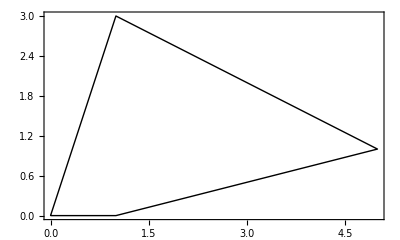

```mathematica
Show[Graphics[Line[AppendTo[poly, First[poly]]]], Frame-> True]
```

```mathematica
areafunction[poly]
```

15/2

## generate a tissue and find area of individual cells

```mathematica
w=TemplateRandomSquareGrid[9, {0,0}, {10,10}];
```

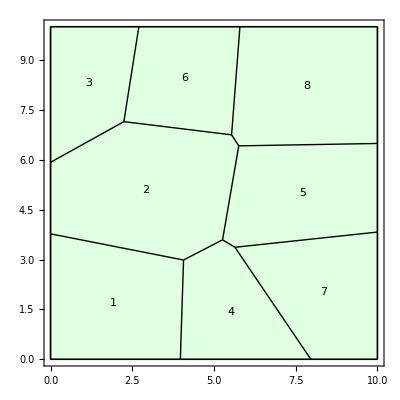

```mathematica
ShowTissue[w, Frame-> True, "CellNumbers"-> True]
```

### get area of all cells in the tissue

```mathematica
areafunction[w]
```

{13.6015,18.8351,8.4304,9.30239,12.8557,9.82151,11.7691,15.3842}

### get area of cell number 2

```mathematica
areafunction[w,2]
```

18.8351